# Tarea 1 Electromagnetismo 1

Diego Sarceño 201900109

## Problema 5

### Distribución n = 3

```mathematica
ϵ=8.85*10^-12
```

8.85×10^-12

```mathematica
a = .
```

```mathematica
Manipulate[VectorPlot[{(q/(4*π*ϵ))*((x+(√3)/2*a)/(((x+(√3)/2*a)^2+(y+a/2)^2)^(3/2))+x/(((x-(√3)/2*a)^2+(y+a/2)^2)^(3/2))+(x-(√3)/2*a)/(((x-(√3)/2*a)^2+(y+a/2)^2)^(3/2))),(q/(4*π*ϵ))*((y+1/2*a)/(((x+(√3)/2*a)^2+(a/2+y)^2)^(3/2))+(a+y)/(((x-(√3)/2*a)^2+(y+a/2)^2)^(3/2))+(y+1/2*a)/(((x-(√3)/2*a)^2+(y+a/2)^2)^(3/2)))},{x,-1,1},{y,-1,1}],{q,0.1,10},{a,0,1}]
```

```mathematica
q=5*10^-6
```

1/200000

```mathematica
ϕ = q/(4π*ϵ)*(1/(√((y-a)^2+x^2))+1/(√((x+(√3)/2*a)^2+(y+1/2*a)^2))+1/(√((x-(√3)/2*a)^2+(y+1/2*a)^2)))
```

8.9918×10^9 q (1/(√(x^2+(-a+y)^2))+1/(√((-(√3 a)/2+x)^2+(a/2+y)^2))+1/(√(((√3 a)/2+x)^2+(a/2+y)^2)))

```mathematica
Grad[-ϕ,{x,y}]
```

{-44959. (-x/((x^2+(a-y)^2)^(3/2))-(-(√3 a)/2+x)/(((-(√3 a)/2+x)^2+(a/2+y)^2)^(3/2))-((√3 a)/2+x)/((((√3 a)/2+x)^2+(a/2+y)^2)^(3/2))),-44959. ((a-y)/((x^2+(a-y)^2)^(3/2))-(a/2+y)/(((-(√3 a)/2+x)^2+(a/2+y)^2)^(3/2))-(a/2+y)/((((√3 a)/2+x)^2+(a/2+y)^2)^(3/2)))}

```mathematica
a = 1
```

1

```mathematica
NSolve[-8.991804694457365*10^8 (-x/((x^2+(a-y)^2)^(3/2))-(-(√3 a)/2+x)/(((-(√3 a)/2+x)^2+(a/2+y)^2)^(3/2))-((√3 a)/2+x)/((((√3 a)/2+x)^2+(a/2+y)^2)^(3/2)))==0&&-8.991804694457365*10^8 ((a-y)/((x^2+(a-y)^2)^(3/2))-(a/2+y)/(((-(√3 a)/2+x)^2+(a/2+y)^2)^(3/2))-(a/2+y)/((((√3 a)/2+x)^2+(a/2+y)^2)^(3/2)))==0,{x,y},Reals]//MatrixForm
```

(y→0.142359 | x→-0.246573
y→0.142359 | x→-0.246573
y→0.142359 | x→0.246573
y→0.142359 | x→0.246573
y→0 | x→0
y→0 | x→0
y→0 | x→0)

NIntegrate::itraw: Raw object -0.999857 cannot be used as an iterator.

General::stop: Further output of NIntegrate::itraw will be suppressed during this calculation.

Integrate::ilim: Invalid integration variable or limit(s) in {-0.857,(√3 a)/2,-0.857}.

General::stop: Further output of StyleBox[RowBox[{\"Integrate\", \"::\", \"ilim\"}], \"MessageName\"] will be suppressed during this calculation.

### Distribución n = 4

```mathematica
ϵ=8.85*10^-12
```

8.85×10^-12

```mathematica
q=5*10^-6
```

1/200000

Potencial Eléctrico:

```mathematica
ϕ = q/(4π*ϵ)*(1/(√((y-(√2)/2*a)^2+(x+(√2)/2*a)^2))+1/(√((x+(√2)/2*a)^2+(y+(√2)/2*a)^2))+1/(√((x-(√2)/2*a)^2+(y+(√2)/2*a)^2))+1/(√((x-(√2)/2*a)^2+(y-(√2)/2*a)^2)))
```

44959. (1/(√((-1/(√2)+x)^2+(-1/(√2)+y)^2))+1/(√((1/(√2)+x)^2+(-1/(√2)+y)^2))+1/(√((-1/(√2)+x)^2+(1/(√2)+y)^2))+1/(√((1/(√2)+x)^2+(1/(√2)+y)^2)))

Calculando el Campo:

```mathematica
Grad[-ϕ,{x,y}]
```

{-44959. (-(-1/(√2)+x)/(((-1/(√2)+x)^2+(-1/(√2)+y)^2)^(3/2))-(1/(√2)+x)/(((1/(√2)+x)^2+(-1/(√2)+y)^2)^(3/2))-(-1/(√2)+x)/(((-1/(√2)+x)^2+(1/(√2)+y)^2)^(3/2))-(1/(√2)+x)/(((1/(√2)+x)^2+(1/(√2)+y)^2)^(3/2))),-44959. (-(-1/(√2)+y)/(((-1/(√2)+x)^2+(-1/(√2)+y)^2)^(3/2))-(-1/(√2)+y)/(((1/(√2)+x)^2+(-1/(√2)+y)^2)^(3/2))-(1/(√2)+y)/(((-1/(√2)+x)^2+(1/(√2)+y)^2)^(3/2))-(1/(√2)+y)/(((1/(√2)+x)^2+(1/(√2)+y)^2)^(3/2)))}

```mathematica
{- (-(-1/(√2)+x)/(((-1/(√2)+x)^2+(-1/(√2)+y)^2)^(3/2))-(1/(√2)+x)/(((1/(√2)+x)^2+(-1/(√2)+y)^2)^(3/2))-(-1/(√2)+x)/(((-1/(√2)+x)^2+(1/(√2)+y)^2)^(3/2))-(1/(√2)+x)/(((1/(√2)+x)^2+(1/(√2)+y)^2)^(3/2))), -(-(-1/(√2)+y)/(((-1/(√2)+x)^2+(-1/(√2)+y)^2)^(3/2))-(-1/(√2)+y)/(((1/(√2)+x)^2+(-1/(√2)+y)^2)^(3/2))-(1/(√2)+y)/(((-1/(√2)+x)^2+(1/(√2)+y)^2)^(3/2))-(1/(√2)+y)/(((1/(√2)+x)^2+(1/(√2)+y)^2)^(3/2)))}
```

$Aborted

Resolviendo el sistema de ecuaciones:

```mathematica
NSolve[{-(-1/(√2)+x)/(((-1/(√2)+x)^2+(-1/(√2)+y)^2)^(3/2))-(1/(√2)+x)/(((1/(√2)+x)^2+(-1/(√2)+y)^2)^(3/2))-(-1/(√2)+x)/(((-1/(√2)+x)^2+(1/(√2)+y)^2)^(3/2))-(1/(√2)+x)/(((1/(√2)+x)^2+(1/(√2)+y)^2)^(3/2))==0,-(-1/(√2)+y)/(((-1/(√2)+x)^2+(-1/(√2)+y)^2)^(3/2))-(-1/(√2)+y)/(((1/(√2)+x)^2+(-1/(√2)+y)^2)^(3/2))-(1/(√2)+y)/(((-1/(√2)+x)^2+(1/(√2)+y)^2)^(3/2))-(1/(√2)+y)/(((1/(√2)+x)^2+(1/(√2)+y)^2)^(3/2))==0},{x,y},Reals]//MatrixForm
```

### Distribución n=5

```mathematica
ϵ=8.85*10^-12
```

8.85×10^-12

```mathematica
q=5*10^-6
```

1/200000

```mathematica
a=.
```

Potencial eléctrico

```mathematica
ϕ = q/(4π*ϵ)*(1/(√((y-a)^2+x^2))+1/(√((x+0.951*a)^2+(y-0.309*a)^2))+1/(√((x+0.588*a)^2+(y+0.809*a)^2))+1/(√((x-0.588*a)^2+(y+0.809*a)^2))+1/(√((x-0.951*a)^2+(y-0.309*a)^2)))
```

8.9918×10^9 q (1/(√(x^2+(-a+y)^2))+1/(√((-0.951 a+x)^2+(-0.309 a+y)^2))+1/(√((0.951 a+x)^2+(-0.309 a+y)^2))+1/(√((-0.588 a+x)^2+(0.809 a+y)^2))+1/(√((0.588 a+x)^2+(0.809 a+y)^2)))

Encontrando el campo

```mathematica
Grad[-ϕ,{x,y}]
```

{-8.9918×10^9 q (-x/((x^2+(-a+y)^2)^(3/2))-(-0.951 a+x)/(((-0.951 a+x)^2+(-0.309 a+y)^2)^(3/2))-(0.951 a+x)/(((0.951 a+x)^2+(-0.309 a+y)^2)^(3/2))-(-0.588 a+x)/(((-0.588 a+x)^2+(0.809 a+y)^2)^(3/2))-(0.588 a+x)/(((0.588 a+x)^2+(0.809 a+y)^2)^(3/2))),-8.9918×10^9 q (-(-a+y)/((x^2+(-a+y)^2)^(3/2))-(-0.309 a+y)/(((-0.951 a+x)^2+(-0.309 a+y)^2)^(3/2))-(-0.309 a+y)/(((0.951 a+x)^2+(-0.309 a+y)^2)^(3/2))-(0.809 a+y)/(((-0.588 a+x)^2+(0.809 a+y)^2)^(3/2))-(0.809 a+y)/(((0.588 a+x)^2+(0.809 a+y)^2)^(3/2)))}

Resolviendo el sistema de ecuaciones

```mathematica
a=1
```

1

```mathematica
y=.
```

```mathematica
x=.
```

```mathematica
NSolve[{-x/((x^2+(-1+y)^2)^(3/2))-(-0.951+x)/(((-0.951+x)^2+(-0.309+y)^2)^(3/2))-(0.951+x)/(((0.951+x)^2+(-0.309+y)^2)^(3/2))-(-0.588+x)/(((-0.588+x)^2+(0.809+y)^2)^(3/2))-(0.588+x)/(((0.588+x)^2+(0.809+y)^2)^(3/2))==0,-(-1+y)/((x^2+(-1+y)^2)^(3/2))-(-0.309+y)/(((-0.951+x)^2+(-0.309+y)^2)^(3/2))-(-0.309+y)/(((0.951+x)^2+(-0.309+y)^2)^(3/2))-(0.809+y)/(((-0.588+x)^2+(0.809+y)^2)^(3/2))-(0.809+y)/(((0.588+x)^2+(0.809+y)^2)^(3/2))==0},{x,y},Reals]//MatrixForm
```

```mathematica
NSolve[Grad[-ϕ,{x,y}],{x,y},Reals]//MatrixForm
```

## Imagenes para el Reporte.

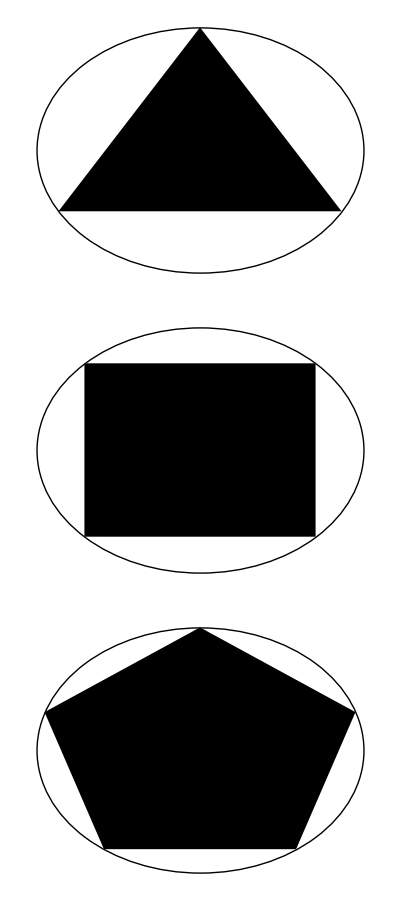
(-Graphics-)

```mathematica
Graphics[{RegularPolygon[{0,0},1,#],Circle[{0,0},1]}]&/@Range[3,5]//MatrixForm
```

## Problema 6: Plots

#### Inciso a)

Campo Dentro de la Esfera:

```mathematica
E=-Grad[-1/2*A*√(x^2+y^2),{x,y}]
```

Set::wrsym: Symbol ⅇ is Protected.

{(A x)/(2 √(x^2+y^2)),(A y)/(2 √(x^2+y^2))}

```mathematica
Manipulate[VectorPlot[{(A x)/(2 √(x^2+y^2)),(A y)/(2 √(x^2+y^2))},{x,-1,1},{y,-1,1}],{A,0,10}]
```

Potencial Dentro de la Esfera:

```mathematica
Manipulate[Plot3D[-1/2*A*√(x^2+y^2),{x,-1,1},{y,-1,1}],{A,0,10}]
```

Campo Fuera de la Esfera:

```mathematica
R=1
```

1

```mathematica
E=-Grad[(A*R^2)/(2*ϵ*√(x^2+y^2)),{x,y}]
```

Set::wrsym: Symbol ⅇ is Protected.

{(5.64972×10^10 A x)/((x^2+y^2)^(3/2)),(5.64972×10^10 A y)/((x^2+y^2)^(3/2))}

```mathematica
Manipulate[VectorPlot[{(5.649717514124294*10^10 *A *x)/((x^2+y^2)^(3/2)),(5.649717514124294*10^10* A *y)/((x^2+y^2)^(3/2))},{x,-1,1},{y,-1,1},VectorColorFunction-> Hue],{A,0,10}]
```

Potencial fuera de la Esfera:

```mathematica
Manipulate[Plot3D[(A*R^2)/(2*ϵ*√(x^2+y^2)),{x,-1,1},{y,-1,1}],{A,0,10}]
```

#### Inciso b)

Campo dentro de la esfera:

```mathematica
ρ=5*10^-9
```

1/200000000

```mathematica
E=Grad[(ρ*(x^2+y^2))/(6*ϵ),{x,y}]
```

Set::wrsym: Symbol ⅇ is Protected.

{188.324 x,188.324 y}

```mathematica
VectorPlot3D[{188.3239171374765*x,188.3239171374765*y,188.3239171374765*z},{x,-1,1},{y,-1,1},{z,-1,1},VectorColorFunction->Hue]
```

-Graphics3D-

Potencial dentro de la esfera:

```mathematica
Plot3D[-(ρ*(x^2+y^2))/(6*ϵ),{x,-1,1},{y,-1,1}]
```

-Graphics3D-

Campo fuera de la esfera:

```mathematica
R=5
```

5

```mathematica
E=Grad[-(ρ*R^3)/(3*ϵ*√(x^2+y^2)),{x,y}]
```

Set::wrsym: Symbol ⅇ is Protected.

{(188.324 x)/((x^2+y^2)^(3/2)),(188.324 y)/((x^2+y^2)^(3/2))}

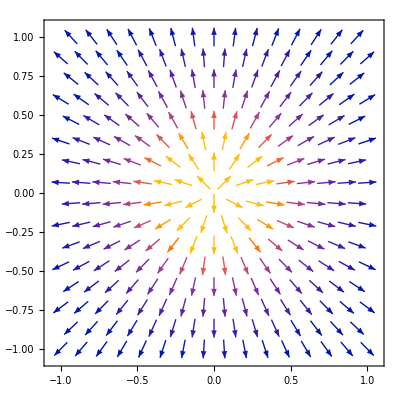

```mathematica
VectorPlot[{(188.3239171374765*x)/((x^2+y^2)^(3/2)),(188.3239171374765*y)/((x^2+y^2)^(3/2))},{x,-1,1},{y,-1,1}]
```

```mathematica
Plot3D[(ρ*R^3)/(3*ϵ*√(x^2+y^2)),{x,-1,1},{y,-1,1}]
```

-Graphics3D-

### Plots como funciones simples:

Inciso a)

```mathematica
A =10
```

10

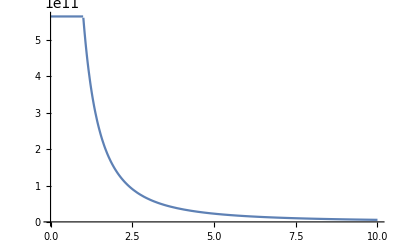

```mathematica
Plot[Piecewise[{{1/(2*ϵ)*A,0≤x<R},{(A*R^2)/(2*ϵ*x^2),R≤x}}],{x,0,10}]
```

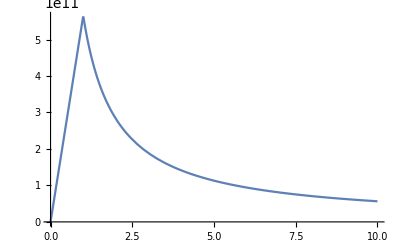

```mathematica
Plot[Piecewise[{{1/(2*ϵ)*A*x,0≤x<R},{(A*R^2)/(2*ϵ*x),R≤x}}],{x,0,10}]
```

Inciso b)

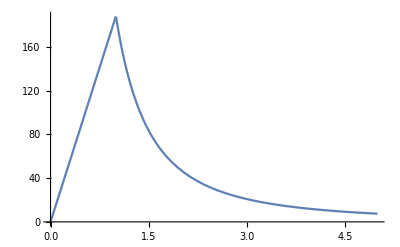

```mathematica
Plot[Piecewise[{{(ρ*x)/(3*ϵ),0≤x<R},{(ρ*R^3)/(3*ϵ*x^2),R≤x}}],{x,0,5}]
```

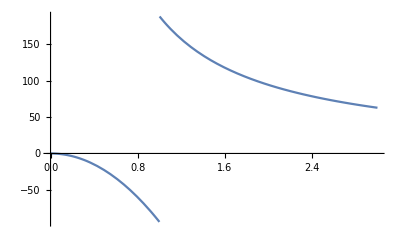

```mathematica
Plot[Piecewise[{{(-ρ*x^2)/(6*ϵ),0≤x<R},{(ρ*R^3)/(3*ϵ*x),R≤x}}],{x,0,3}]
```

## Problema 10: Plots

#### Inciso a)

```mathematica
a=2
```

2

```mathematica
b=4
```

4

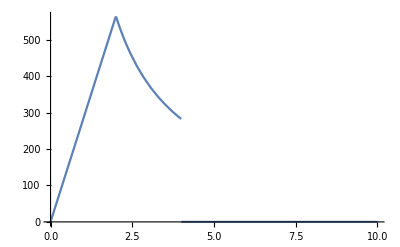

Set::wrsym: Symbol ⅇ is Protected.

```mathematica
Plot[Piecewise[{{(ρ*x)/(2*ϵ),0≤x<a},{(ρ*a^2)/(2*ϵ*x),a≤x<b},{0,x≥b}}],{x,0,10}]
```